FittedModel[1.12196^x]

{1.12196^x}

-0.142207

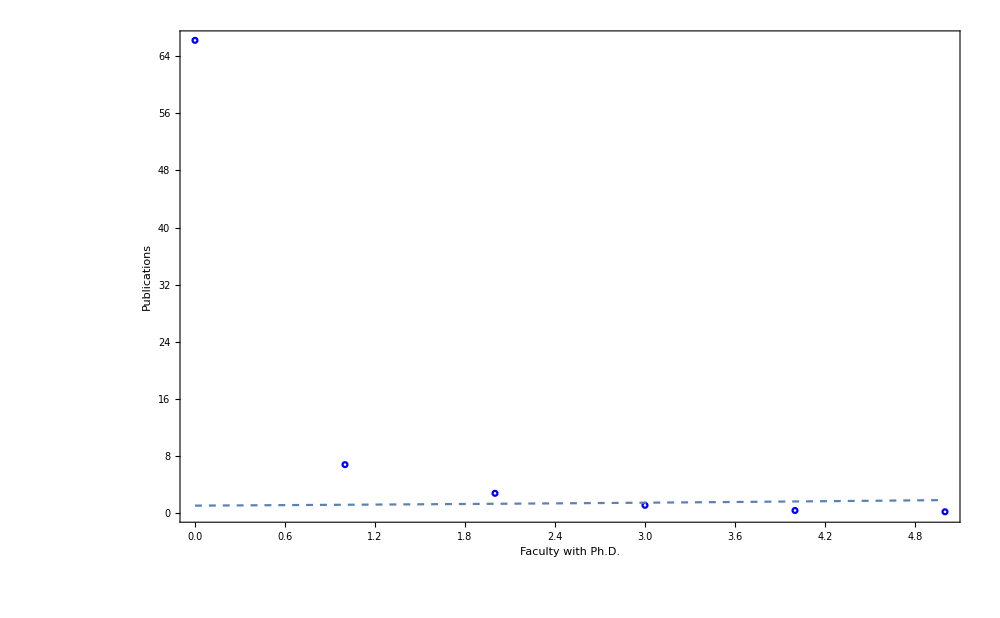

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados/ConCompetencia";
SetDirectory["/home/fabianact/ActualTesis/Tesis/ModelosPresentados/Distribución"];
SetOptions[BarChart,BaseStyle->{FontSize->18}];
data1 = Import[y<>"/averageResults/data-0.001-100-pro-true-turtles.csv"];
data1 = data1[[1;;6]];
lm1=NonlinearModelFit[Flatten[data1],(a  b) ^ (x ),{a,b},x]
P1=lm1[{"BestFit"}]
R21=lm1["AdjustedRSquared"]
plot1=Show[ListPlot[{data1}, PlotRange->All, PlotStyle->{Blue},PlotMarkers->{Graphics[{Circle[]},ImageSize-> 5]}],Plot[lm1[x],{x,0,Max[data1[[All, 1]]]}, PlotStyle->{Dashed}], AxesLabel->{"Profesores", "Publicaciones"},ImageSize->1000, Frame->True,FrameLabel->{Style["Faculty with Ph.D.",Black,Large],Style["Publications",Black,Large]}]
```